# Alphabet for all 9 point sub-kinematics

Load all the data about the 9-particle alphabet and its invariant subspace

```mathematica
SetDirectory[NotebookDirectory[]];
(* 9-point rational alphabet *)
<<Gr49RationalDCI.m;
(* 9-point algebraic alphabet *)
<<algebraicLettersRepresentatives.m;
(* Rational and algebraic alphabet subspace invariant under certain differential operators*)
<<"nullSpaceData.m";
```

The notebook is structure as follows:

-The chapter Functions must be compiled at the start and contains all the Mathematica functions need to run the notebook. Some of the functions are commented and come with an example.

-The chapter Main result shows the use of the two main functions rationalSubAlphabet[kinematics] and algebraicSubAlphabet[kinematics], the notation, and how to test numerically the consistency of their output. It further contains application thereof for the cases at interest in this work.

-The chapter Further properties and demo of useful functions shows how discrete symmetries act on the 9-particle alphabet, how to extract the null space of one or multiple Z_i∂_j operators. Finally we show by explicit computation that an algebraic letter can have non-trivial projection to the Z_i∂_j nullspace if and only if its root is invariant under Z_i∂_j

## Functions

### Front end

```mathematica
(* Here are a series of function to display momentum brackets in a nice form. Expressions with cap cannot be copypasted.
Examples:
Input: br[1,2,3,4]
Output: 1234
Input:cap[{1,2,3},{4,5,6},{7,8}]
Output:⟨(123)∩(456)∩(78)⟩
*)
```

```mathematica
Clear[brBox]
brBox[a_,b__] := 
 TemplateBox[{b}, "br", 
  DisplayFunction -> (  TemplateBox[{"⟨",b,"⟩"},"RowDefault"] &), 
  InterpretationFunction ->(RowBox[{"br","[",a[[1,2]],"]"}]&)]

Clear[br]
br /: MakeBoxes[br[xx__], StandardForm | TraditionalForm] := brBox[ToBoxes@{xx},Sequence@@(ToBoxes/@{xx})]
```

```mathematica
Clear[capBox]
capBox[a_,b__] := 
 TemplateBox[{b}, "cap", 
  DisplayFunction -> (  TemplateBox[{"⟨",Sequence@@b,"⟩"},"RowDefault"] &), 
  InterpretationFunction ->(RowBox[{"cap","[",a[[1,2]],"]"}]&)]

Clear[cap]
cap /: MakeBoxes[cap[xx__], StandardForm | TraditionalForm] := brBox[ToBoxes[{xx}],Sequence@@capToBoxes[{xx}]]
```

```mathematica
Clear[capToBoxes]
capToBoxes[list__]:=Module[{temp},
temp=Insert[#,"(",1]&/@list;
temp=Insert[#,")",-1]&/@temp;
temp=(ToBoxes/@(Flatten@Insert[temp,"∩",List/@Range[2,Length[temp]]]))
]
```

### X Parametrization

```mathematica
Z9clus=Transpose@{{1,0,0,0,-1,-1-x[1]-x[1]*x[2]-x[1]*x[2]*x[3],-1-x[1]-x[1]*x[2]-x[1]*x[2]*x[3]-x[1]*x[4]-x[1]*x[2]*x[4]-x[1]*x[2]*x[3]*x[4]-x[1]*x[2]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6],-1-x[1]-x[1]*x[2]-x[1]*x[2]*x[3]-x[1]*x[4]-x[1]*x[2]*x[4]-x[1]*x[2]*x[3]*x[4]-x[1]*x[2]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]-x[1]*x[4]*x[7]-x[1]*x[2]*x[4]*x[7]-x[1]*x[2]*x[3]*x[4]*x[7]-x[1]*x[2]*x[4]*x[5]*x[7]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]-x[1]*x[2]*x[4]*x[5]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[9],-1-x[1]-x[1]*x[2]-x[1]*x[2]*x[3]-x[1]*x[4]-x[1]*x[2]*x[4]-x[1]*x[2]*x[3]*x[4]-x[1]*x[2]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]-x[1]*x[4]*x[7]-x[1]*x[2]*x[4]*x[7]-x[1]*x[2]*x[3]*x[4]*x[7]-x[1]*x[2]*x[4]*x[5]*x[7]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]-x[1]*x[2]*x[4]*x[5]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[9]-x[1]*x[4]*x[7]*x[10]-x[1]*x[2]*x[4]*x[7]*x[10]-x[1]*x[2]*x[3]*x[4]*x[7]*x[10]-x[1]*x[2]*x[4]*x[5]*x[7]*x[10]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]*x[10]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[10]-x[1]*x[2]*x[4]*x[5]*x[7]*x[8]*x[10]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]*x[8]*x[10]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[10]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[9]*x[10]-x[1]*x[2]*x[4]*x[5]*x[7]*x[8]*x[10]*x[11]-x[1]*x[2]*x[3]*x[4]*x[5]*x[7]*x[8]*x[10]*x[11]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[10]*x[11]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[9]*x[10]*x[11]-x[1]*x[2]*x[3]*x[4]*x[5]*x[6]*x[7]*x[8]*x[9]*x[10]*x[11]*x[12]},{0,1,0,0,1,1+x[1]+x[1]*x[2],1+x[1]+x[1]*x[2]+x[1]*x[4]+x[1]*x[2]*x[4]+x[1]*x[2]*x[4]*x[5],1+x[1]+x[1]*x[2]+x[1]*x[4]+x[1]*x[2]*x[4]+x[1]*x[2]*x[4]*x[5]+x[1]*x[4]*x[7]+x[1]*x[2]*x[4]*x[7]+x[1]*x[2]*x[4]*x[5]*x[7]+x[1]*x[2]*x[4]*x[5]*x[7]*x[8],1+x[1]+x[1]*x[2]+x[1]*x[4]+x[1]*x[2]*x[4]+x[1]*x[2]*x[4]*x[5]+x[1]*x[4]*x[7]+x[1]*x[2]*x[4]*x[7]+x[1]*x[2]*x[4]*x[5]*x[7]+x[1]*x[2]*x[4]*x[5]*x[7]*x[8]+x[1]*x[4]*x[7]*x[10]+x[1]*x[2]*x[4]*x[7]*x[10]+x[1]*x[2]*x[4]*x[5]*x[7]*x[10]+x[1]*x[2]*x[4]*x[5]*x[7]*x[8]*x[10]+x[1]*x[2]*x[4]*x[5]*x[7]*x[8]*x[10]*x[11]},{0,0,1,0,-1,-1-x[1],-1-x[1]-x[1]*x[4],-1-x[1]-x[1]*x[4]-x[1]*x[4]*x[7],-1-x[1]-x[1]*x[4]-x[1]*x[4]*x[7]-x[1]*x[4]*x[7]*x[10]},{0,0,0,1,1,1,1,1,1}};
```

### Evaluation and differential operators

#### Evaluation of any function

```mathematica
(*evalNum[fun,var,range] give the expression fun where all variables var are evaluated on random integers.  
Example
evalNum[x[1],{x[1]},{0,3}]
Out: random number from 0 to 3*)
```

```mathematica
Clear[evalNum,withBlockedVars]
evalNum[fun_,var_,range_List:{1,10}]:=Module[{myBlock,typeVar=DeleteDuplicates@Cases[var,f_[___]:>  f]},
myBlock=Hold[typeVar]/. OwnValues[typeVar]/. Hold[typeVar_]:>withBlockedVars[typeVar];
myBlock[var=RandomInteger[range,Length[var]];fun]
]

withBlockedVars=Function[vars,Function[code,Block[vars,code],HoldAll],HoldAll];
```

#### Evaluation, sorting br

```mathematica
(* evalBr[exp,Zparam] parametrize an expression of 4-brackets using the momentum twistor coorinates Zparam
Input: evalBr[br[1,2,3,4],Z9clus]
Out: 1*)
```

```mathematica
evalBr[exp_,Zparam_]:=Block[{br,allbrs}, allbrs=Flatten[Table[br[i,j,k,l],{i,Length[Zparam]},{j,i+1,Length[Zparam]},{k,j+1,Length[Zparam]},{l,k+1,Length[Zparam]}]];
Thread[set[allbrs,Factor[Det[(Zparam[[{##}]])]&@@@allbrs]]]/.set-> Set;
exp
]
```

```mathematica
(* evalCap[exp] expand the intersection of planes in a momentum twistors bracket polynomial. Works only for the intersection of 2 3-planes and a 2-plane or 4 3-planes;
Input: evalCap[cap[{1,2,3},{4,5,6},{7,8}]];
Out: 1238 4567-1237 4568;
Input:evalCap[cap[{1,2,3},{4,5,6},{7,8,9},{a,b,c}]];
Output:-1236 (4abc 5789-4789 5abc)+1235 (4abc 6789-4789 6abc)-1234 (5abc 6789-5789 6abc)
*)
```

```mathematica
evalCap[cap[{1,2,3},{4,5,6},{7,8,9},{a,b,c}]]
```

-1236 (4abc 5789-4789 5abc)+1235 (4abc 6789-4789 6abc)-1234 (5abc 6789-5789 6abc)

```mathematica
Clear[evalCap]
SetAttributes[evalCap,Listable]
evalCap[exp_]:=Block[{cap},cap[{a__},{b__},{c1_,c2_}]:=br[a,c1]br[c2,b]- br[a,c2]br[c1,b] /.sortbr;
cap[a_List,b_List,c_List,d_List]:=Sum[(-1)^i (br@@Append[a,b[[i]]])cap[ c,d,Delete[b,i]],{i,3}]/.sortbr;exp]
```

```mathematica
(*sortbr order the arguments of br
Input: br[2,1]/. sortbr
Out -12*)
```

```mathematica
sortbr={br[z__]:>Signature[{z}] br@@Sort[{z}]};
```

```mathematica
(*fastSortbr[exp] order the arguments of br
Input: fastSortbr[br[2,1]]
Out -12*)
```

```mathematica
Clear[fastSortbr]
fastSortbr[exp_]:=Block[{br},br[z__]:=Signature[{z}] br@@Sort[{z}]/;!(Sort[{z}]==={z});exp ]
```

#### Differential operators

```mathematica
Clear[Op]
Op[i_,j_][a_+b_]:=Op[i,j][a]+Op[i,j][b]
Op[i_,j_][a_ b_]:=Op[i,j][a]b+Op[i,j][b] a 
Op[i_,j_][x_^pow_]:=Op[i,j][x]pow x^(pow-1)
Op[i_,j_][x_?NumericQ]:=0
Op[i_,j_][br[x__]]:=Op[i,j][br[x]]=If[Or[!MemberQ[{x},j],MemberQ[{x},i]],0,Signature[#/.j->i]br@@Sort[#]&@({x}/.j->i)]
Op[i_,j_][Log[standardBlock[a_,b_,Sqrt[c_]]]]:=(-2 b c Op[i,j][a]+2 a c Op[i,j][b]+a b Op[i,j][c])/((a^2-b^2 c)Sqrt[c])
Op[i_,j_][Log[x_]]:=Op[i,j][x]/x
```

### Logs manipulation

```mathematica
(*CollectRemoveLogs[exp] write a linear combinations of logarithms as the argument of a single Log up to an over all numerical factor.
Input:CollectRemoveLogs[2Log[a]+Log[b]+Log[3]]
Output:a^2 b
*)
```

```mathematica
Clear[CollectRemoveLogs]
CollectRemoveLogs[exp_]:=Block[{myLog=Identity},#]&@Block[{Log=myLog},exp];
```

```mathematica
SetAttributes[myLog,Listable]
myLog[x_]/;NumericQ[x]:=0
myLog/:Times[a_,myLog[x_] ]:=myLog[x^a]
myLog/:Plus[myLog[a_],myLog[b_] ]:=myLog[a b]
```

### Cyclic Transformations and reflection

```mathematica
allCyclicPerm[n_]:=Thread[Rule[Range[n],#]]&/@Permute[Range[n],CyclicGroup[n]];
```

```mathematica
allCyclicDihedralperm[n_]:=Thread[Rule[Range[n],#]]&/@Join[Permute[Range[n],CyclicGroup[n]],Reverse/@Permute[Range[n],CyclicGroup[n]]];
```

```mathematica
cyclicPerm[n_]:=Thread@Rule[ Range[n],RotateLeft[Range[n]]]
```

```mathematica
(*permuteBrAndCap[exp,permRule] permutes all 4brackets and cap accorting to the permutation exp*;
Input: permuteBrAndCap[{br[1,2,3,4],cap[{1,2,3},{4,5,6},{8,9}]},cyclicPerm[9]];
Output: {br[2,3,4,5],cap[{2,3,4},{5,6,7},{9,1}]}*)
```

```mathematica
permuteBrAndCap[exp_,permRule_List]:=Block[{brTemp=br,capTemp=cap},#]&@Block[{br,cap},brTemp[z__]:=Signature[{z}] brTemp@@Sort[{z}]/;!(Sort[{z}]==={z});br[x__]:=brTemp[x]/.permRule;cap[x__]:=capTemp[x]/.permRule;exp]
```

```mathematica
invarsePermRule[perm_List]:=Reverse/@perm
```

### Extract Alphabet from nullspace

#### Generic Functions

```mathematica
(*operatorsFromKinematics[kinematics] gives a list containing operators that characterize the kinematic configuration given in the variable kinematics. The operators are represented as Op[i,j]-> {i,j} .
Input: operatorsFromKinematics[{1,{2,3},4,5,6,7,8,9}]
Output: {{1,2},{4,3}}*)
```

```mathematica
operatorsFromKinematics[kinematics_List]:=Module[{n=Length[Flatten@kinematics]},Flatten[{{Mod[#[[1]]-1,n,1],#[[1]]},{Mod[#[[2]]+1,n,1],#[[2]]}}&/@Select[kinematics,Head[#]===List&],1]];
```

```mathematica
(* equationsFromKinematics[kinematics,alphabet] gives a list of expression that must vanish for expression to be well defined on the kinematic given by the variable kinematics.
```

```mathematica
equationsFromKinematics[kinematics_List,expression_List]:=equationsFromKinematics[kinematics,#]&/@expression

equationsFromKinematics[kinematics_List,expression_]:=#[expression]&/@(Op@@@operatorsFromKinematics[kinematics])
```

```mathematica
(*myIntersectionBasis[lists] find the intersection between the vector spaces contained in lists. The result is given as a SparseArray.
Example: Normal@myIntersectionBasis[{{{1,0,0},{0,1,0}},{{0,1,0},{0,0,1}}}]
Out: {{0,1,0}}*)
```

```mathematica
Clear[myIntersectionBasis]
myIntersectionBasis[lists_List]:={}/;MemberQ[lists,{}]
myIntersectionBasis[lists_List]:=Module[{temp,ortogonalSpace},
ortogonalSpace=Join@@(NullSpace[#,Method->"OneStepRowReduction"]&/@lists);
If[ortogonalSpace==={},Return[First[lists]]];
temp=NullSpace[ortogonalSpace,Method->"OneStepRowReduction"];
If[temp==={},{},SparseArray@temp]
]
```

#### Rational Alphabet

```mathematica
Clear[rationalNullspace]
rationalNullspace[i_Integer,i_Integer]:=$Failed;
rationalNullspace[i_Integer,j_Integer]:=rationalNullspace[i,j]=rationalNullspace[i,j]=Module[{sign,ii,jj,power},
If[And[i===9,j===1],Return[rationalNullSpace12.MatrixPower[cycleGr49RationalDCI,8]]];
sign=True;
ii=i;jj=j;
If[Or[i>j,And[i===1,j===9]],sign=False;ii=Mod[-i,9,1];jj=Mod[-j,9,1]];
power=ii-1;
If[sign, rationalNullSpace12. MatrixPower[ cycleGr49RationalDCI,power],
rationalNullspace[ii,jj].flipGr49rationalDCI
]
]
```

```mathematica
Clear[rationalAlphabetSubspace]
rationalAlphabetSubspace[kinematics_List]:=rationalAlphabetSubspace[kinematics]=Module[{operators,n=Length[Flatten@kinematics]},myIntersectionBasis@(rationalNullspace@@@operatorsFromKinematics[kinematics])]
```

```mathematica
rationalSubAlphabet[kinematics_List]:=CollectRemoveLogs[rationalAlphabetSubspace[kinematics].(Log/@Gr49RationalDCI)]
```

#### Algebraic Alphabet

```mathematica
algebraicAlphabet=Flatten[Table[NestList[permuteBrAndCap[#,cyclicPerm[9]]&,algebraicLettersRepresentatives[[i]],8],{i,36}],1];
```

```mathematica
Clear[algebraicAlphabetRepresentativesSubspace]
algebraicAlphabetRepresentativesSubspace[k_,kinematics_List]:=algebraicAlphabetRepresentativesSubspace[k,kinematics]=Module[{operators,n=Length[Flatten@kinematics]},myIntersectionBasis@(algebraicNullSpaceRepresentatives[k]@@@operatorsFromKinematics[kinematics])]
```

```mathematica
algebraicSubAlphabet[kinematics_List]:=Flatten[Table[Table[permuteBrAndCap[ddot[algebraicAlphabetRepresentativesSubspace[i,kinematics/.perm],Log[algebraicLettersRepresentatives[[i]]]],invarsePermRule[perm]],{perm,allCyclicPerm[9]}],{i,36}],1]
```

```mathematica
ddot[{},y_]:={}
ddot[x_,y_]:=x.y
```

```mathematica
(*findRoots[x] gives a list of all different square roots that appear in x at arbitrary depth.;
Input: findRoots[1+Sqrt[xx]];
Output: {√xx}*)
findRoots[x_]:=DeleteDuplicates@Cases[x,Sqrt[a_],∞]
```

### Find Symmetries

```mathematica
findSymmetries[term_,potentialSymmetries_]:=Module[{actionSymmetries,numericEval,allOperators},
allOperators=Op@@@potentialSymmetries;
actionSymmetries=ParallelMap[#[term]&,allOperators,ProgressReporting->False];
numericEval=evalBr[evalCap@actionSymmetries,evalNum[Z9clus,x/@Range[12]]];
Extract[potentialSymmetries,Position[numericEval,0]]
]
```

### Graph from Kinematics

```mathematica
ClearAll[graphFromKinematics];

graphFromKinematics[l_List]:=Module[{n,groups,lens,labelsOuter,inner,outer,innerEdges,outerEdges,innerAngles,innerCoords,outerCoords,coords,R=2,Δ,x},
x=Replace[Reverse@l,y_List:>Reverse[y],{1}];
n=Length[x];
groups=Replace[x,a_/;AtomQ[a]:>{a},{1}];
lens=Length/@groups;
labelsOuter=Flatten[x];
Δ=Min[Pi/6,2 Pi/n];
inner=Array[i,n];
outer=Array[o,Length@labelsOuter];
innerEdges=UndirectedEdge@@@Partition[Append[inner,First@inner],2,1];
outerEdges=Flatten@MapThread[Thread[#1->#2]&,{inner,TakeList[outer,lens]}];
innerAngles=Table[2 Pi (k-1)/n,{k,n}];
innerCoords=Thread[inner->({Cos[#],Sin[#]}&/@innerAngles)];
outerCoords=Flatten@MapThread[Function[{θ,outs},Module[{m=Length@outs,offs},offs=If[m==1,{0},Subdivide[-Δ/2,Δ/2,m-1]];
Thread[outs->(R {Cos[θ+#],Sin[θ+#]}&/@offs)]]],{innerAngles,TakeList[outer,lens]}];
coords=Join[innerCoords,outerCoords];
Graph[Join[innerEdges,outerEdges],VertexCoordinates->coords,VertexLabels->Thread[outer->(Style[#,White]&/@labelsOuter)],VertexShapeFunction->None,VertexSize->0,EdgeShapeFunction->"Line",EdgeStyle->{DirectedEdge[_,_]->Arrowheads[0.03]}]];
```

## Main results

## Sub-kinematic rational alphabet

The 9-particle rational alphabet is contained in the variable Gr49RationalDCI

```mathematica
Gr49RationalDCI[[1]]
Gr49RationalDCI//Length
```

(1239 1248)/(1234 1289)

3078

The alphabet for a general kinematic can be extracted using the function rationalSubAlphabet[kinematics]. We represent massive external legs with a pair of massless legs. For example, the DCI kinematics of 5-point with 4 adjacent massive legs is represented by the list

```mathematica
kinematics={{1,2},{3,4},{5,6},{7,8},9};
```

and the correspondent sub-alphabet is given by

```mathematica
(pentagon4Masses=rationalSubAlphabet[kinematics])//Short
```

{1/(1239 2345^2 6789^2)2367 (-1389 2359 2459 4678+1289 2359 3459 4678+1389 2359 2458 4679-1289 2359 3458 4679+1389 2349 2459 5678-1289 2349 3459 5678-1389 2349 2458 5679+1289 2349 3458 5679),1/(1239^2 4567^2 6789)2367 (1457 1689 2359 4679-1456 1789 2359 4679+1235 1789 4569 4679-1235 1689 4579 4679-1457 1689 2349 5679+1456 1789 2349 5679-1234 1789 4569 5679+1234 1689 4579 5679),-(1789 2356 4679-1689 2357 4679-1789 2346 5679+1689 2347 5679)/(1239 4567 6789),(1389 2359 2467-1389 2349 2567-1289 2359 3467+1289 2349 3567)/(1239 2345 6789),(2367 («1») (2359 4679-2349 5679))/(1239^2 2345 4567 6789^2),(2367«1»«1»)/(«1»),«1»,-(2367 («1»))/(1239 2345 6789),(2389 4567)/(2345 6789),(1679 2345)/(1239 4567),(1459 2367)/(1239 4567),(2367 4589)/(2345 6789)}

The subspace of the rational alphabet  consistent with a certain kinematic configuration can be extracted using the function rationalSubAlphabet[kinematics].

```mathematica
invariantSubspace=rationalAlphabetSubspace[kinematics]
```

SparseArray[…]

We can obtain the same result as rationalSubAlphabet[kinematics] by projecting the alphabet on invariantSubspace, collecting the argument of the Logs and removing the Logs

```mathematica
reducedRationalAlphabet=invariantSubspace.Log[Gr49RationalDCI];
```

```mathematica
Thread[pentagon4Masses==CollectRemoveLogs[reducedRationalAlphabet]]
```

True

We can test the result using the function equationsFromKinematics[kinematics,alphabet]. An alphabet for a kinematic with massive external legs must be invariant under the operators

```mathematica
Op@@@operatorsFromKinematics[kinematics]
```

{Op[9,1],Op[3,2],Op[2,3],Op[5,4],Op[4,5],Op[7,6],Op[6,7],Op[9,8]}

where Op[i,j] indicates the differential operator Z_i∂_j. The correspondent differential equations that the letters must satisfy are given by

```mathematica
equation=equationsFromKinematics[kinematics,Log@pentagon4Masses];
```

Note that the argument of equationsFromKinematics are the letters with the Log. We can evaluate the action of the operators numerically using the Z9clus parametrizatin as follows and check that the result is consistent

```mathematica
test=evalBr[equation,evalNum[Z9clus,x/@Range[12]]];
DeleteDuplicates@Flatten@test
```

{0}

## Sub-kinematic algebraic alphabet

The algebraic Alphabet is represented by the variable algebraicAlphabet. Letters with the same square root are collected  in a list. There are 324 lists in  algebraicAlphabet . Each letters is written in the form standardBlock[a,b,√c], which represent the expression (a+b√c)/(a-b √c) . For example

```mathematica
algebraicAlphabet[[1,1]]
```

standardBlock[-1239 (1378 2467-1278 3467)^2+1237^2 1789 2346 4678+(1236 1478-1234 1678) 2378 (1467 2379-1237 4679),1237 (178)∩(237)∩(46),√(-4 1239 1789 2346 4678+(-1789 2346+1469 2378-1239 4678)^2)]

Letters have 4-brackets where intersection of planes are present, for example ⟨(178)∩(237)∩(46)⟩. The correspondent InputForm is cap[{1,7,8},{2,3,7},{4,6}]. The notation for the intersection is as follow

(ab)~(ab)_KL=Z_a^I Z_b^J ϵ_IJKL
(abc)~(abc)_L=Z_a^I Z_b^J Z_c^K ϵ_IJKL

brackets of this form can be written as polynomials in ordinary  4-brackets with the command evalCap

```mathematica
cap[{1,7,8},{2,3,7},{4,6}]
evalCap@%
```

(178)∩(237)∩(46)

-1678 2347+1478 2367

Nb : outputs with 4-brackets can be copy-pasted while outputs with caps cannot.

The alphabet for a general kinematic can be extract using the function algebraicSubAlphabet[kinematics]. For example, the DCI kinematics of 5-point with 4 adjacent massive legs is represented by the list

```mathematica
kinematics={{1,2},{3,4},{5,6},{7,8},9};
```

```mathematica
Flatten[algebraicSubAlphabet[kinematics]]//Short
%//Length
```

{-Log[standardBlock[-2345 2389 4567 4789^2+(-2789 3457+2457 3789) 4589 (-2347 4689+2346 4789)+(2489 3457-2457 3489)^2 6789,-4789 (745)∩(894)∩(23),√(-4 2345 2389 4567 6789+(2389 4567-2367 4589+2345 6789)^2)]]+Log[«1»]+Log[standardBlock[(-2789 3459+2459 3789)^2 4567-(-2789 3457+2457 3789) 4589 (-2359 4679+2349 5679)-2345 2389 4579^2 6789,4579 (789)∩(923)∩(45),√(-4 2345 2389 4567 6789+(2389 4567-2367 4589+2345 6789)^2)]],«6»,Log[«1»]+«1»}

8

```mathematica
algebraicPentagon4Masses=algebraicSubAlphabet[kinematics];
```

We can test the result using the function equationsFromKinematics[kinematics,alphabet]. This gives one equation for each shift operator that characterize the kinematics. This time we need to apply the function to each group of letters with the same root separately

```mathematica
temp=Log[evalCap@DeleteCases[algebraicPentagon4Masses,{}]]/.standardBlock[a_,b_,c_]-> (a+b c)/(a-b c);
equation=equationsFromKinematics[kinematics,#]&/@%;
```

Then we need to evaluate the action of the operators numerically

```mathematica
test=evalBr[equation,evalNum[Z9clus,x/@Range[12]]];
res=DeleteDuplicates@Flatten@FullSimplify[test]
```

{0}

## Examples

We demonstrate the relevant subkinematics of this work. These are the cases where two massive legs are adjacent and the DCI breaking limit x_i→infinity can be considered to get LI letters. Both rational and algebraic subalphabets are considered.

### 7-point-2mass DCI

The first relevant case at hand is the one of 7-point-2-mass DCI kinematics, it can be visualized with graphFromKinematics. The subalphabet of this kinematic is equivalent to the one of 6-point-1mass LI one.

```mathematica
kinematics7M2={2,3,4,5,6,{7,8},{9,1}};
```

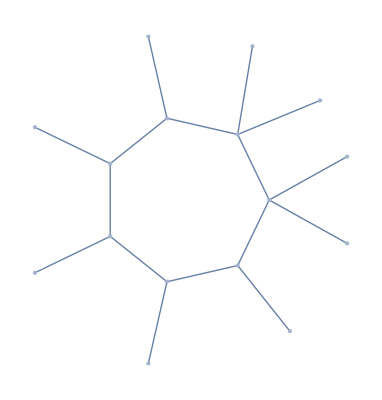

```mathematica
graphFromKinematics[kinematics7M2]
```

```mathematica
rationalSubAlphabet[kinematics7M2]//Flatten//Short
%//DeleteDuplicates//Length
```

{1/(1256 1289 2345^2 3456 6789^3)2689^2 (-1239 1789 2345 3568+1239 1345 2789 3568+1238 1789 2345 3569-1238 1345 2789 3569+1239 1689 2345 3578-1239 1345 2689 3578-1238 1689 2345 3579+1238 1345 2689 3579) 4567^2,-1/(1256 1289 2345^2 3456 6789^3)1234 2689^2 4567 (1789 2359 3456 5678-1359 2789 3456 5678-1689 2359 3457 5678+1359 2689 3457 5678-1789 2358 3456 5679+1358 2789 3456 5679+1689 2358 3457 5679-1358 2689 3457 5679),«174»,(1234 1256 4589 6789)/(1289^2 3456 4567),(1289^2 2367 3456 4567)/(1234 1256 2345 6789^2)}

178

```mathematica
algebraicSubAlphabet[kinematics7M2]//Flatten//Short
%//DeleteDuplicates//Length
```

{Log[standardBlock[-1235 (1689 2367-1367 2689)^2-1267 (1269 3568-1268 3569) (1239 3678-1238 3679)+1236^2 1289 3567 6789,1236 (968)∩(126)∩(37),√(-4 1235 1289 3567 6789+(1289 3567-1267 3589+1235 6789)^2)]],«66»,Log[standardBlock[((1239 1678-1238 1679) 2356+1356 (-1239 2678+1238 2679)) ((1267 2345-1257 2346) 2689+1256 2346 2789)+1256 (1239 2678-1238 2679)^2 3456-1234 1267 1289 2356^2 6789,2356 (231)∩(267)∩(89),√((«1»)^2-4 1234 1256 1267 1289 3456 6789)]]}

68

### 6-point-3mass DCI

#### Medium

The second relevant case will be that of 6- point-3 mass medium kinematics, it is equivalent to the 5-point-2-mass Easy LI one.

```mathematica
kinematics6M3M={2,3,{4,5},6,{7,8},{9,1}};
```

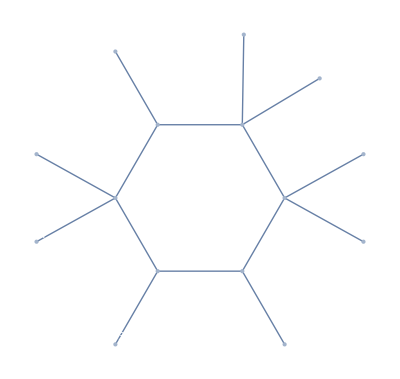

```mathematica
graphFromKinematics[kinematics6M3M]
```

```mathematica
rationalSubAlphabet[kinematics6M3M]//Flatten//Short
%//DeleteDuplicates//Length
algebraicSubAlphabet[kinematics6M3M]//Flatten//Short
%//DeleteDuplicates//Length
```

{-1/(1256 1289 3456 6789)(1269 1689 2345 5678-1259 1689 2346 5678-1269 1345 2689 5678+1259 1346 2689 5678-1268 1689 2345 5679+1258 1689 2346 5679+1268 1345 2689 5679-1258 1346 2689 5679),1/(1289^2 2567 3456^2)1256 (1249 2349 3568 5678-1249 2348 3569 5678-1239 2349 4568 5678+1239 2348 4569 5678-1248 2349 3568 5679+1248 2348 3569 5679+1238 2349 4568 5679-1238 2348 4569 5679),(1267 1689 2345 2356-1257 1689 2346 2356+1256 1789 2346 2356-1267 1356 2345 2689+1257 1356 2346 2689-1256 1356 2346 2789)/(1256 1289 2367 3456),«46»,(1234 2689 3567)/(1289 2367 3456),(1256 3489)/(1289 3456),(1267 1289 3456)/(1234 1256 6789)}

52

{Log[standardBlock[-1234 2356 (1689 2367-1367 2689)^2-1267 2346 (1269 3568-1268 3569) (1239 3678-1238 3679)+1236^2 1289 2346 3567 6789,1236 (968)∩(126)∩(37),√(-4 1234 1289 2346 2356 3567 6789+(1289 2346 3567+1267 2349 3568-1267 2348 3569+1234 2356 6789)^2)]],«17»,Log[standardBlock[((1239 1678-1238 1679) 2356+1356 (-1239 2678+1238 2679)) ((1267 2345-1257 2346) 2689+1256 2346 2789)+1256 (1239 2678-«1»)^2 3456-1234 1267 1289 2356^2 6789,2356 (231)∩(267)∩(89),√((«1»)^2-«1»)]]}

19

#### Hard

Finally, we present the 6-point-3-mass hard kinematic alphabet that is equivalent to the 5-point-2-mass Hard LI one. Note that there are two pairs of adjacent massive legs here, therefore two choices for the infinity twistor.

```mathematica
kinematics6M3H={2,3,4,{5,6},{7,8},{9,1}};
```

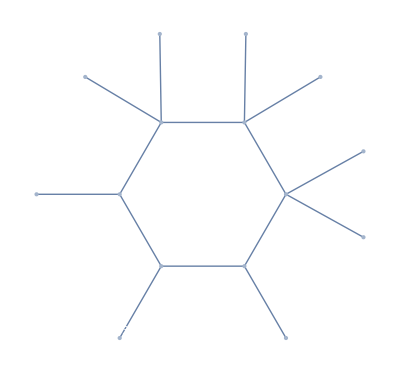

```mathematica
graphFromKinematics[kinematics6M3H]
```

```mathematica
rationalSubAlphabet[kinematics6M3H]//Flatten//Short
%//DeleteDuplicates//Length
algebraicSubAlphabet[kinematics6M3H]//Flatten//Short
%//DeleteDuplicates//Length
```

{-1/(1234^2 2345 6789^3)1289 2367 (1249 3457 3689 4678-1249 3456 3789 4678-1248 3457 3689 4679+1248 3456 3789 4679-1239 3457 4678 4689+1238 3457 4679 4689+1239 3456 4678 4789-1238 3456 4679 4789),-1/(1289^2 2367 4567^2)(-1235 1789 2456 2467+1235 1689 2457 2467+1234 1789 2456 2567-1234 1689 2457 2567-1235 1467 2457 2689+1234 1567 2457 2689+1235 1467 2456 2789-1234 1567 2456 2789) 6789,«47»,(1267 2345 6789)/(1289 2367 4567),(2367 4589)/(2345 6789)}

51

{«1»}

23

## Further properties and demo of useful functions

## Alphabet Structure and discrete symmetries

### Rational Alphabet

```mathematica
ruleDihedral={1->8,2->7,3->6,4->5,5->4,6->3,7->2,8->1,9->9};
```

```mathematica
cyclicPerm[9]={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->9,9->1};
```

The action of these symmetries is saved in “Gr49RationalDCI.m”  in the varaibles cycleGr49RationalDCI and flipGr49rationalDCI. These are two permutations implemented as matrices and can be used as follows

```mathematica
cyclicPermutedAlphabet=Gr49RationalDCI.cycleGr49RationalDCI;
dihedralPermutedAlphabet=Gr49RationalDCI.flipGr49rationalDCI ;
```

In a nutshell, every 9 consecutive letters of Gr49RationalDCI form a cyclic multiplet, and in total we have 342 of them . 28 of these are also dihedral multiplets, namely the flip maps them back into themselves; the rest pair up to form another 157 dihedral multiplets, i . e . a total of 185 dihedral multiplets .

### Algebraic Alphabet

The algebraic alphabet is generated by the action of the cyclic symmetry from a group of representatives contained in the variable. These have been extracted from https://arxiv.org/abs/2106.01392 and massaged such that letters characterized by the same square root manifestly have the same square root.

The letters in algebraicLettersRepresentatives are grouped in 36 classes.

```mathematica
algebraicLettersRepresentatives//Length
```

36

Each class have just 1 square root. findRoots[x] gives a list of all different square roots that appear in x at arbitrary depth. We can use it to check that we indeed have just 1 root per class.

```mathematica
(allRoots=findRoots/@algebraicLettersRepresentatives)//Short
Length/@%
```

{{√(-4 1239 1789 2346 4678+(-1789 2346+1469 2378-1239 4678)^2)},«34»,{√((-1235 1789 2346 5789+1234 1789 2356 5789+1235 1469 2378 5789-1234 1569 2378 5789-1235 1239 4678 5789+1234 1239 5678 5789+1235 1789 2345 6789-1235 1459 2378 6789+1235 1239 4578 6789)^2-4 (1235^2 1239 1789 2346 4678 5789^2-1234 1235 1239 1789 2356 4678 5789^2-1234 1235 1239 1789 2346 5678 5789^2+1234^2 1239 1789 2356 5678 5789^2-1235^2 1239 1789 2346 4578 5789 6789+1234 1235 1239 1789 2356 4578 5789 6789-1235^2 1239 1789 2345 4678 5789 6789+1234 1235 1239 1789 2345 5678 5789 6789+1235^2 1239 1789 2345 4578 6789^2))}}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

The full alphabet is generated from algebraicLettersRepresentatives through cyclic permutation and saved in algebraicAlphabet. Also in this case,  every 9 consecutive classes of algebraicAlphabet form a cyclic multiplet.

We can test this by using the function permuteBrAndCap[exp,perm]

```mathematica
Thread[permuteBrAndCap[algebraicAlphabet[[1]],cyclicPerm[9]]==algebraicAlphabet[[2]]]
```

True

It is a fact that no roots are invariant under cyclic symmetry, therefore the number of total classes is given by 36 x 9 =324

```mathematica
Length@algebraicAlphabet
```

324

Regarding the action of the dihedral flip, its precise action is not implemented in this notebook. Nevertheless, here is a list describing how classes in algebraicLettersRepresentatives are related by the dihedral flip

```mathematica
{{1},{9},{30},{31},{35},{36},{2,13},{3,12},{4,22},{5,15},{6,14},{7,16},{8,23},{10,17},{11,25},{18,24},{19,26},{20,21},{27,28},{29,32},{33,34}}
```

{{1},{9},{30},{31},{35},{36},{2,13},{3,12},{4,22},{5,15},{6,14},{7,16},{8,23},{10,17},{11,25},{18,24},{19,26},{20,21},{27,28},{29,32},{33,34}}

Single indices indicate that the class map to itself under the dihedral flip, while pairs of indices indicate that the two classes are related by a dihedral flip.

## Differential shift operators and their null spaces

The differential operator Z_i∂_j is encoded in the operator Op[i,j]

```mathematica
Op[1,2]@2345
```

1345

Because of the planar amplitude discrete symmetries, we can derive the subspaces invariant under a general shift operator Z_i∂_j, that is Op[i,j] , form the subspace invariant under Op[1,2] which is saved for the rational alphabet in rationalNullSpace12.

```mathematica
rationalNullSpace12
```

SparseArray[…]

The generic nullspace of the operator Op[i,j] is saved in rationalNullspace[i,j]

```mathematica
rationalNullspace[3,2]
```

SparseArray[…]

For the algebraic alphabet the function algebraicNullSpaceRepresentatives[k][i,j] gives the null space of the operator Op[i,j] in the class k of algebraicLettersRepresentatives

```mathematica
algebraicNullSpaceRepresentatives[1][2,3]
```

SparseArray[…]

The nullspace of multiple operators can be derived by intersecting null spaces of a single operator

```mathematica
myIntersectionBasis[{rationalNullspace[1,2],rationalNullspace[2,1]}]
```

SparseArray[…]

## Reducibility of algebraic letters

We prove by explicit computation that an algebraic alphabet class, that is the set of letters with the same square root, has a non-trivial nullspace under Op[i,j], if and only if, the root that characterize the class vanish under Op[i,j]

All possible shift operators are

```mathematica
allShifts=Join[#,Reverse/@#]&@Partition[Append[Range[9],1],{2},1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,1},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{1,9}}

Let define a function that gives the argument of the square root of the class k

```mathematica
argumentRootClass[k_]:= algebraicLettersRepresentatives[[k,1,3,1]]
```

a function that gives the non trivial null spaces of class k

```mathematica
nonTriavialNullspaces[k_]:= Select[allShifts,!(algebraicNullSpaceRepresentatives[k][Sequence@@#]==={})&]
```

And we have already implemented a function that findSymmetries[exp,shiftsList] that gives all the shifts in shiftsList that live exp invariant

```mathematica
findSymmetries[argumentRootClass[1],allShifts]
nonTriavialNullspaces[1]
```

{{2,3},{4,5},{7,8},{9,1},{3,2},{6,5},{8,7},{1,9}}

{{2,3},{4,5},{7,8},{9,1},{3,2},{6,5},{8,7},{1,9}}

Then we simply check the equality for all the 36 class in  algebraicLettersRepresentatives

```mathematica
Table[findSymmetries[argumentRootClass[k],allShifts]===nonTriavialNullspaces[k],{k,36}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}